3 - 12 Effect of delta (impulse) on vibrating systems
Find and graph or sketch the solution of the IVP.

3.  y'' + 4 y = δ (t - π),  y[0] = 8, y'[0] = 0

```mathematica
Clear["Global`*"]
```

```mathematica
e1=LaplaceTransform[y''[t]+4 y[t]==DiracDelta[ (t-π)],t,s]
```

4 LaplaceTransform[y[t],t,s]+s^2 LaplaceTransform[y[t],t,s]-s y[0]-y'[0]==ⅇ^(-π s)

```mathematica
e2=e1/.{y[0]->8,y'[0]->0,LaplaceTransform[y[t],t,s]->bigY}
```

4 bigY-8 s+bigY s^2==ⅇ^(-π s)

```mathematica
e3=Solve[e2,bigY]
```

{{bigY→(ⅇ^(-π s) (1+8 ⅇ^(π s) s))/(4+s^2)}}

```mathematica
e4=e3[[1,1,2]]
```

(ⅇ^(-π s) (1+8 ⅇ^(π s) s))/(4+s^2)

```mathematica
e5=InverseLaplaceTransform[e4,s,t]
```

8 Cos[2 t]+Cos[t] HeavisideTheta[-π+t] Sin[t]

```mathematica
PossibleZeroQ[Cos[t]Sin[t]-1/2 Sin[2t]]
```

True

I showed in section 6.3 that HeavisideTheta is equivalent to UnitStep. Combined with the PZQ above, it makes the green cell equivalent to the text answer.

```mathematica
plot1=Plot[e5,{t,0,3 π},PlotRange->Automatic,PlotStyle->{Yellow,Thickness[0.003]},ImageSize->250];
plot2=Plot[8 Cos[2 t]+1/2 UnitStep[t-π] Sin[2 t],{t,0,3 π},PlotRange->Automatic,PlotStyle->{Red,Thickness[0.01]},ImageSize->250];
```

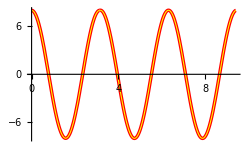

```mathematica
Show[plot2,plot1]
```

Above: The solution tracks well with that of the text.

5.  y'' + y = δ (t - π) - δ (t - 2 π), y[0] = 0, y'[0] = 1

```mathematica
Clear["Global`*"]
```

```mathematica
e1=LaplaceTransform[y''[t]+y[t]==DiracDelta[t-π]-DiracDelta[t-2 π],t,s]
```

LaplaceTransform[y[t],t,s]+s^2 LaplaceTransform[y[t],t,s]-s y[0]-y'[0]==-ⅇ^(-2 π s)+ⅇ^(-π s)

```mathematica
e2=e1/.{y[0]->0,y'[0]->1,LaplaceTransform[y[t],t,s]->bigY}
```

-1+bigY+bigY s^2==-ⅇ^(-2 π s)+ⅇ^(-π s)

```mathematica
e3=Solve[e2,bigY]
```

{{bigY→(ⅇ^(-2 π s) (-1+ⅇ^(π s)+ⅇ^(2 π s)))/(1+s^2)}}

```mathematica
e4=e3[[1,1,2]]
```

(ⅇ^(-2 π s) (-1+ⅇ^(π s)+ⅇ^(2 π s)))/(1+s^2)

```mathematica
e5=InverseLaplaceTransform[e4,s,t]
```

-(-1+HeavisideTheta[-2 π+t]+HeavisideTheta[-π+t]) Sin[t]

```mathematica
e6=e5/.{HeavisideTheta[-2 π+t]->0,HeavisideTheta[-π+t]->0}
```

Sin[t]

Above: The answer agrees with the text for the subinterval t<π.

```mathematica
e7=e5/.{HeavisideTheta[-2 π+t]->0,HeavisideTheta[-π+t]->1}
```

0

Above: The answer agrees with the text for the subinterval π<t<2π.

```mathematica
e8=e5/.{HeavisideTheta[-2 π+t]->1,HeavisideTheta[-π+t]->1}
```

-Sin[t]

Above: The answer agrees with the text for the subinterval t>2π.

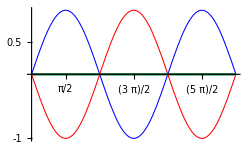

```mathematica
plot1=Plot[{e6,e7,e8},{t,0,3 π},PlotRange->Automatic,PlotStyle->{{Blue,Thickness[0.003]},{RGBColor[0.1,0.5,0.3],Thickness[0.007]},{Red,Thickness[0.003]}},ImageSize->250,Ticks->{{π/2,π,(3π)/2,2π,(5π)/2,3π},{-1,-.5,.5,1}},GridLines->{{π/2,π,(3π)/2,2π,(5π)/2,3π},{-1,-.5,.5,1}}]
```

7.  4y''+24y'+37y=17 ⅇ^-t+δ(t-1/2), y[0]=1, y'[0]=1

```mathematica
Clear["Global`*"]
```

```mathematica
e1=LaplaceTransform[4 y''[t]+24 y'[t]+37 y[t]==17 ⅇ^-t +DiracDelta[t-1/2],t,s]
```

37 LaplaceTransform[y[t],t,s]+24 (s LaplaceTransform[y[t],t,s]-y[0])+4 (s^2 LaplaceTransform[y[t],t,s]-s y[0]-y'[0])==ⅇ^(-s/2)+17/(1+s)

```mathematica
e2=e1/.{y[0]->1,y'[0]->1,LaplaceTransform[y[t],t,s]->bigY}
```

37 bigY+24 (-1+bigY s)+4 (-1-s+bigY s^2)==ⅇ^(-s/2)+17/(1+s)

```mathematica
e3=Solve[e2,bigY]
```

{{bigY→(28+ⅇ^(-s/2)+4 s+17/(1+s))/(37+24 s+4 s^2)}}

```mathematica
e4=e3[[1,1,2]]
```

(28+ⅇ^(-s/2)+4 s+17/(1+s))/(37+24 s+4 s^2)

```mathematica
e5=InverseLaplaceTransform[e4,s,t]
```

1/4 ⅇ^(-ⅈ/4-(3+ⅈ/2) t) (4 ⅇ^(ⅈ/4) (2 ⅈ-2 ⅈ ⅇ^(ⅈ t)+ⅇ^((2+ⅈ/2) t))+ⅈ ⅇ^(3/2) (ⅇ^(ⅈ/2)-ⅇ^(ⅈ t)) HeavisideTheta[-1/2+t])

```mathematica
e6=FullSimplify[e5]
```

1/2 ⅇ^(-3 t) (2 ⅇ^(2 t)-ⅇ^(3/2) HeavisideTheta[-1/2+t] Sin[1/4 (1-2 t)]+8 Sin[t/2])

```mathematica
e7=Expand[e6]
```

ⅇ^-t-1/2 ⅇ^(3/2-3 t) HeavisideTheta[-1/2+t] Sin[1/4 (1-2 t)]+4 ⅇ^(-3 t) Sin[t/2]

```mathematica
PossibleZeroQ[(ⅇ^-t-1/2 ⅇ^(3/2-3 t)  Sin[1/4 (1-2 t)]+4 ⅇ^(-3 t) Sin[t/2])-(ⅇ^-t+4 ⅇ^(-3t)Sin[1/2 t]+1/2(ⅇ^(-3(t-1/2))Sin[1/2 t-1/4]))]
```

True

Above: By comparison of plots in section 6.3 I decided that HeavisideTheta is equivalent to UnitStep, the function the text prefers to use. Granted that equivalence, the PZQ above confirms that the green cell is equivalent to the text answer.

```mathematica
plot1=Plot[e7,{t,0,1},PlotRange->Automatic,PlotStyle->{Yellow,Thickness[0.002]},ImageSize->250];
plot2=Plot[ⅇ^-t+4 ⅇ^(-3 t) Sin[t/2]+1/2 UnitStep[t-1/2] ⅇ^(-3(t-1/2))Sin[t/2-1/4],{t,0,1},PlotRange->Automatic,PlotStyle->{Red,Thickness[0.008]},ImageSize->250];
```

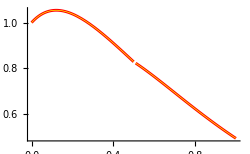

```mathematica
Show[plot2,plot1]
```

Note the interesting little gap which seems to exist in the combined plot above.

```mathematica
plot3=Plot[e7,{t,0.45,0.55},PlotRange->Automatic,PlotStyle->{Green,Thickness[0.003]},ImageSize->250];
```

```mathematica
plot5=Plot[ⅇ^-t+4 ⅇ^(-3 t) Sin[t/2]+1/2 UnitStep[t-1/2] ⅇ^(-3(t-1/2))Sin[t/2-1/4],{t,0.45,0.55},PlotRange->Automatic,PlotStyle->{Red,Thickness[0.01]},ImageSize->250];
```

In zoomed view, there is a slight dogleg bend, but no gap. WolframAlpha rules that e7 is continuous on ℝ, so I don’t know what the problem is with plotting the superposition.

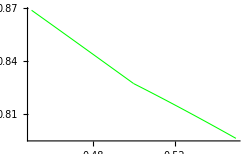
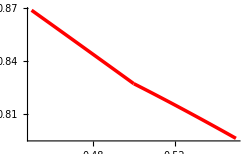
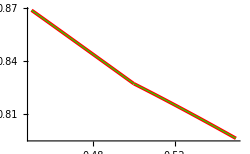

```mathematica
Row[{plot3,plot5,Show[plot5,plot3]}]
```

9.  y''+4y'+5y=(1-u(t-10))ⅇ^t-ⅇ^10 δ(t-10),  y[0]=0, y'[0]=1

```mathematica
Clear["Global`*"]
```

I try again with the method of the last two problems, but this one is harder.

```mathematica
e1=LaplaceTransform[y''[t]+ 4 y'[t]+ 5 y[t]==(1-UnitStep[t-10])ⅇ^t-ⅇ^10 DiracDelta[t-10],t,s]
```

5 LaplaceTransform[y[t],t,s]+s^2 LaplaceTransform[y[t],t,s]+4 (s LaplaceTransform[y[t],t,s]-y[0])-s y[0]-y'[0]==-ⅇ^(10-10 s)+1/(-1+s)-ⅇ^(-10 (-1+s))/(-1+s)

Above: The Laplace transform is similar to the one in the last problem, as a term containing s has been placed in the denominator of the rhs. I use the same ploy as in the past to isolate the expression I need for the reverse transform.

```mathematica
e2=e1/.{y[0]->0,y'[0]->1,LaplaceTransform[y[t],t,s]->bigY}
```

-1+5 bigY+4 bigY s+bigY s^2==-ⅇ^(10-10 s)+1/(-1+s)-ⅇ^(-10 (-1+s))/(-1+s)

```mathematica
e3=Solve[e2,bigY]
```

{{bigY→(ⅇ^(-10 s) (-ⅇ^10+ⅇ^(10 s)) s)/((-1+s) (5+4 s+s^2))}}

```mathematica
e4=e3[[1,1,2]]
```

(ⅇ^(-10 s) (-ⅇ^10+ⅇ^(10 s)) s)/((-1+s) (5+4 s+s^2))

I try to get a reverse transfrom from the bigY object, in which all subexpressions are real.

```mathematica
e5=InverseLaplaceTransform[e4,s,t]
```

1/20 ⅇ^((-2-ⅈ) ((2+4 ⅈ)+t)) ((-1-ⅈ) ⅇ^(10 ⅈ) ((-3-4 ⅈ)+(4+3 ⅈ) ⅇ^(2 ⅈ t)-(1-ⅈ) ⅇ^((3+ⅈ) t))+((1-7 ⅈ) ⅇ^(30+20 ⅈ)+(1+7 ⅈ) ⅇ^(30+2 ⅈ t)-2 ⅇ^((3+ⅈ) ((1+3 ⅈ)+t))) HeavisideTheta[-10+t])

But in the result I see there are imaginaries, which, unlike in previous cases, do not disappear after using FullSimplify.

```mathematica
e17=FullSimplify[e5]
```

1/20 ⅇ^((-2-ⅈ) ((2+4 ⅈ)+t)) ((-1-ⅈ) ⅇ^(10 ⅈ) ((-3-4 ⅈ)+(4+3 ⅈ) ⅇ^(2 ⅈ t)-(1-ⅈ) ⅇ^((3+ⅈ) t))+((1-7 ⅈ) ⅇ^(30+20 ⅈ)+(1+7 ⅈ) ⅇ^(30+2 ⅈ t)-2 ⅇ^((3+ⅈ) ((1+3 ⅈ)+t))) HeavisideTheta[-10+t])

So I take a side step to get rid of the imaginaries. Maybe later I can judge whether this is a wise step.

```mathematica
e6=ComplexExpand[Re[e5]];
```

```mathematica
e7=FullSimplify[e6]
```

1/10 ⅇ^(-2 t) (ⅇ^(3 t)-Cos[t]+7 Sin[t]+(-ⅇ^(3 t)+ⅇ^30 (Cos[10-t]+7 Sin[10-t])) UnitStep[-10+t])

Time to bring in the text answer. ( In entering the text answer I changed 0.1 to 1/10 (two occurrences).)

```mathematica
e8=1/10(ⅇ^t+ⅇ^(-2 t) (-Cos[t]+7 Sin[t]))+1/10 UnitStep[t-10] (-ⅇ^-t+ⅇ^(-2 t+30)(Cos[t-10]-7 Sin[t-10]))
```

1/10 (ⅇ^t+ⅇ^(-2 t) (-Cos[t]+7 Sin[t]))+1/10 (-ⅇ^-t+ⅇ^(30-2 t) (Cos[10-t]+7 Sin[10-t])) UnitStep[-10+t]

I see that the text answer comes up with the correct result for one of the initial conditions. The Mathematica answer also gets past this hurdle.

```mathematica
e8t=e8/.t->0
```

0

```mathematica
e7t=e7/.t->0
```

0

```mathematica
N[e7t10=e7/.t->11]
```

-1594.81

```mathematica
plot1=Plot[e7,{t,0,5},PlotRange->Automatic,PlotStyle->{Yellow,Thickness[0.002]},ImageSize->250];
plot2=Plot[e8,{t,0,5},PlotRange->Automatic,PlotStyle->{Red,Thickness[0.014]},ImageSize->250];
plot3=Plot[e17,{t,0,5},PlotRange->Automatic,PlotStyle->{Blue,Thickness[0.006]},ImageSize->250];
```

Plotting all three of the proposed solutions. On the selected interval they all track one other well.

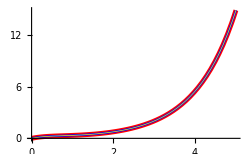

```mathematica
Show[plot2,plot3,plot1]
```

I try subtractive tests but the text answer is not the same as the Mathematica answer. I move on to looking at some more plots.

```mathematica
plot3=Plot[e17,{t,0,15},PlotRange->{{0,13},{-50000,50000}},PlotStyle->{RGBColor[0.4,0.5,1],Thickness[0.007]},ImageSize->350];
plot4=Plot[e8,{t,0,15},PlotRange->Automatic,PlotStyle->{Red,Thickness[0.014]},ImageSize->350];
plot7=Plot[e7,{t,0,15},PlotRange->Automatic,PlotStyle->{White,Thickness[0.003]},ImageSize->350];
```

Plotting a slightly longer interval. It seems I have three different functions. The one that has discarded imaginary elements seems to have, for some reason, a slightly smaller range. However, Wolfram Alpha judges it to be continuous on ℝ. In contrast the text function has a jump discontinuity at t=10.

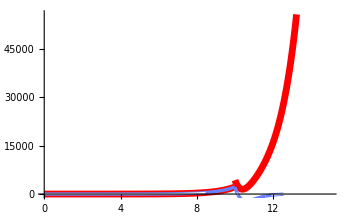

```mathematica
Show[plot4,plot3,plot7]
```

Both the Mathematica (real) solution and the text solution meet the second initial condition.

```mathematica
dp=D[e8,t];
```

```mathematica
dp/.t->0
```

1

```mathematica
dpm=D[e7,t];
```

```mathematica
dpm/.t->0
```

1

So if the Mathematica solution meets both initial conditions, is it considered correct?

11.  y'' + 5 y' + 6 y = u (t - 1) + δ (t - 2),  y[0] = 0, y'[0] = 1

```mathematica
Clear["Global`*"]
```

```mathematica
e1=LaplaceTransform[y''[t]+5 y'[t]+6 y[t]==UnitStep[t-1]+DiracDelta[t-2],t,s]
```

6 LaplaceTransform[y[t],t,s]+s^2 LaplaceTransform[y[t],t,s]+5 (s LaplaceTransform[y[t],t,s]-y[0])-s y[0]-y'[0]==ⅇ^(-2 s)+ⅇ^-s/s

```mathematica
e2=e1/.{y[0]->0,y'[0]->1,LaplaceTransform[y[t],t,s]->bigY}
```

-1+6 bigY+5 bigY s+bigY s^2==ⅇ^(-2 s)+ⅇ^-s/s

```mathematica
e3=Solve[e2,bigY]
```

{{bigY→(ⅇ^(-2 s) (ⅇ^s+s+ⅇ^(2 s) s))/(s (6+5 s+s^2))}}

```mathematica
e4=e3[[1,1,2]]
```

(ⅇ^(-2 s) (ⅇ^s+s+ⅇ^(2 s) s))/(s (6+5 s+s^2))

```mathematica
e5=InverseLaplaceTransform[e4,s,t]
```

1/6 ⅇ^(-3 t) (6 (-1+ⅇ^t)+6 ⅇ^4 (-ⅇ^2+ⅇ^t) HeavisideTheta[-2+t]+(ⅇ-ⅇ^t)^2 (2 ⅇ+ⅇ^t) HeavisideTheta[-1+t])

```mathematica
e6=-ⅇ^(-3 t)+ⅇ^(-2 t)+1/6 UnitStep[t-1] (1-3 ⅇ^(-2 (t-1))+2 ⅇ^(-3 (t-1)))+UnitStep[t-2] (ⅇ^(-2 (t-2))-ⅇ^(-3 (t-2)))
```

-ⅇ^(-3 t)+ⅇ^(-2 t)+(-ⅇ^(-3 (-2+t))+ⅇ^(-2 (-2+t))) UnitStep[-2+t]+1/6 (1+2 ⅇ^(-3 (-1+t))-3 ⅇ^(-2 (-1+t))) UnitStep[-1+t]

Above: The text answer is entered.

```mathematica
plot1=Plot[e5,{t,0,1},PlotRange->Automatic,PlotStyle->{Yellow,Thickness[0.002]},ImageSize->250];
plot2=Plot[e6,{t,0,1},PlotRange->Automatic,PlotStyle->{Red,Thickness[0.008]},ImageSize->250];
```

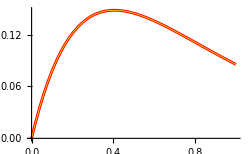

```mathematica
Show[plot2,plot1]
```

Above: the two plots suggest equality.

```mathematica
e7=e6/.UnitStep->HeavisideTheta
```

-ⅇ^(-3 t)+ⅇ^(-2 t)+(-ⅇ^(-3 (-2+t))+ⅇ^(-2 (-2+t))) HeavisideTheta[-2+t]+1/6 (1+2 ⅇ^(-3 (-1+t))-3 ⅇ^(-2 (-1+t))) HeavisideTheta[-1+t]

```mathematica
FullSimplify[e5==e7]
```

True

Above: So: If the UnitSteps are exchanged for Heavisides, the answers match.